# Particle Diffusion

Michael Jones and Ian Jackson

```mathematica
Clear["`*"]
Needs["Units`"]
```

Start by creating a GUI window

```mathematica
DynamicModule[{f,p},f[g_]:=Graphics[g,ImageSize->Tiny];{SetterBar[Dynamic[p],{Disk[]->Disk,Rectangle[]->Rectangle}],Dynamic[f[p]]}]
```

Create a list of constants

```mathematica
k=8.6173*^-5 LinguisticAssistant;
T=300;
atom="Hydrogen";
m=ElementData[atom,"AtomicMass"];
m=UnitConvert[m,"MeV/c^2"];
v=UnitConvert[Sqrt[3 k T/m],"m/s"];
simV=QuantityMagnitude[v]/10000;
R=ElementData[atom,"AtomicRadius"];
simR=QuantityMagnitude[R]/1000;
σ=Pi R^2;
n=1;
width=1;(*Corresponds to um*)
height=1;
If[n>objectMax,n=objectMax];
maxX=Floor[width/(2 simR)];
maxY=Floor[height/(2 simR)];
objectMax=maxX maxY;
```

Create an array of n elements

{{1/3,1/2}}

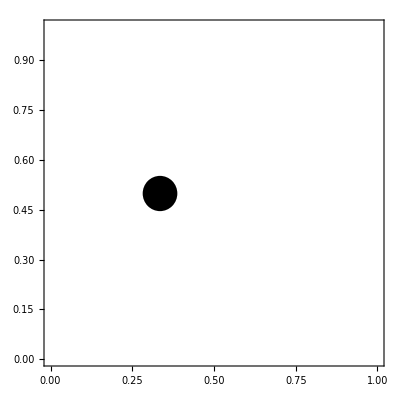

```mathematica
rows=Floor[Sqrt[n]];
cols=rows+1;
stepX=width/(cols+1);
stepY=height/(rows+1);
counterX=stepX;
counterY=stepY;
objectList={};
Do[objectList=Append[objectList,{counterX,counterY}];
counterX=counterX+stepX;
If[counterX>width-simR,counterX=stepX;counterY=counterY+stepY],
n]
objectList
Graphics[{Black,Disk[{#[[1]],#[[2]]},simR]}&/@objectList,PlotRange->{{0,width},{0,height}},Frame->True]
```

```mathematica
tracked=Floor[n/2]+1;
objectV={};
Do[vRatio=RandomReal[{-1,1}];
Vy=((-1)^RandomInteger[1]) simV/Sqrt[vRatio^2+1];
objectV=Append[objectV,{vRatio Vy,Vy}],
n];
```

```mathematica
move[i_]:=Module[{},
If[objectList[[i,1]]>width-simR||objectList[[i,1]]<simR,objectV[[i,1]]=-objectV[[i,1]]];
If[objectList[[i,2]]>height-simR||objectList[[i,2]]<simR,objectV[[i,2]]=-objectV[[i,2]]];
objectList[[i,1]]=objectList[[i,1]]+objectV[[i,1]];
objectList[[i,2]]=objectList[[i,2]]+objectV[[i,2]];
];
```